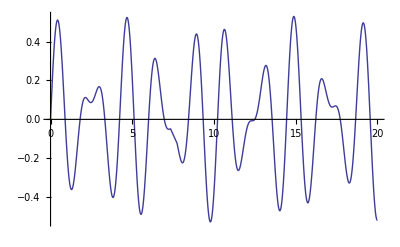

-Graphics-

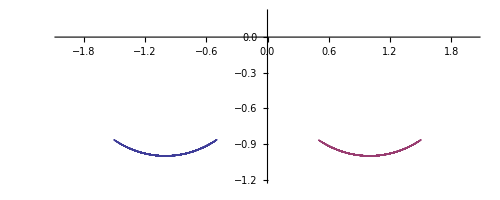

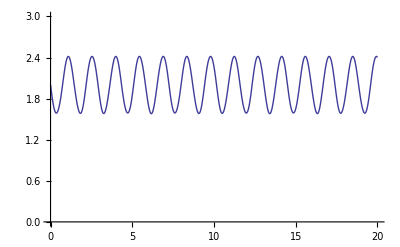

```mathematica
g=9.8;width=2;m1=0.2;m2=0.2;L=1;k=1;tm=20;
initial1={0,1.9/L};initial2={0,0};
L12=√((width+L(Sin[θ2[t]]-Sin[θ1[t]]))^2+L^2(Cos[θ2[t]]-Cos[θ1[t]])^2);
eqs={θ1''[t]==(k(width Cos[θ1[t]]+L Sin[θ2[t]-θ1[t]]))/(m1 L)(1-width/L12)-g/L Sin[θ1[t]],θ2''[t]==(-k(width Cos[θ2[t]]+L Sin[θ2[t]-θ1[t]]))/(m2 L)(1-width/L12)-g/L Sin[θ2[t]],θ1[0]==initial1[[1]],θ1'[0]==initial1[[2]],θ2[0]==initial2[[1]],θ2'[0]==initial2[[2]]};
s=NDSolve[eqs,{θ1,θ2},{t,0,tm}];
{θ1,θ2}={θ1,θ2}/.s[[1]];
Plot[θ1[t],{t,0,tm}]
Plot[θ1[t],{t,0,tm}]
ParametricPlot[Evaluate[{{L Sin[θ1[t]]-width/2,-L Cos[θ1[t]]},{L Sin[θ2[t]]+width/2,-L Cos[θ2[t]]}}],{t,0,tm},PlotRange->{{-width/2-1,width/2+1},{-L-0.2,0.2}}]
Plot[L12,{t,0,tm},PlotRange->{{0,tm},{0,3}}]
```

```mathematica
Clear[g,eqs,s,θ1,θ2,tm,initial1,initial2,k,L,m1,m2,width,L12,n,dt,gif,point1,point2,line1,line2,line3,line4,disk1,disk2,pic]
```

```mathematica
n=2000;dt=tm/n;gif={};
Do[point1={L Sin[θ1[j dt]]-width/2,-L Cos[θ1[j dt]]};point2={L Sin[θ2[j dt]]+width/2,-L Cos[θ2[j dt]]};line1=Graphics[{Dashed,Line[{{-0.2-width/2,0},{0.2+width/2}}]}];line2=Graphics[{Thick,Line[{{-width/2,0},point1}]}];line3=Graphics[{Thick,Line[{{width/2,0},point2}]}];line4=Graphics[{Dashed,Line[{point1,point2}]}];disk1=Graphics[Disk[point1,0.05]];disk2=Graphics[Disk[point2,0.05]];pic=Show[{line1,line2,line3,line4,disk1,disk2},PlotRange->{{-width/2-1,width/2+1},{-L-0.2,0.2}}];AppendTo[gif,pic],{j,0,n}]
Export["e:/1.gif",gif]
```

e:/1.gif